# Bias control of MCHMC

## Expectation values

```mathematica
R[n_]:= If[n==0, 1, (d+n-2)R[n-2]];  (* = <r^n> *)
Nwick[n_]:= If[n==0, 1,(n-1)Nwick[n-2]]; (* number of Wick's contractions for the n-point correlation function*)
A[n_, m_]:=Nwick[m]R[n+m]/R[m]; (* = <r^n (u.x)^m> *)
rules[order_] := Table[r^(2n) xu^(order-2n)-> A[2n,order-2n] , {n,0,order/2}]; (* insert values for = <r^n (u.x)^m> with n+m = order*)
Drule = {D-> d-1};
Allrules[expr_, order_]:= If[order==0, expr, Allrules[expr/.rules[order], order-2]]/.Drule//Simplify;
```

```mathematica
rules[4]
rules[2]
```

{xu^4→3,r^2 xu^2→2+d,r^4→d (2+d)}

{xu^2→1,r^2→d}

## Euler

### Standard Normal

```mathematica
δ = ϵ r / D;
Energy = D Log[Cosh[δ] - xu Sinh[δ]/r] + ϵ^2 / 2 + ϵ xu;
series = Series[Energy, {ϵ, 0, 2}] //Simplify
```

((D+r^2-xu^2) ϵ^2)/(2 D)+O[ϵ]^3

```mathematica
E1 = Allrules[Expand[ SeriesCoefficient[series, 2] ], 2]
```

1

```mathematica
series = Series[Energy^2, {ϵ, 0, 4}] //Simplify
```

((D+r^2-xu^2)^2 ϵ^4)/(4 D^2)+O[ϵ]^5

```mathematica
E2 = Allrules[Expand[ SeriesCoefficient[series, 4] ], 4]
```

(1-2 d)/(2-2 d)

```mathematica
E2 - E1^2 //Simplify
```

1/(2 (-1+d))

### General Gaussian

```mathematica
δ = ϵ Hx / D;
Energy = D Log[Cosh[δ] - uHx Sinh[δ]/Hx] + ϵ^2 uHu/ 2 + ϵ uHx;
Series[Energy, {ϵ, 0, 3}] //Simplify
```

((Hx^2+D uHu-uHx^2) ϵ^2)/(2 D)+(uHx (Hx^2-uHx^2) ϵ^3)/(3 D^2)+O[ϵ]^4

## Leapfrog

### Standard Normal

```mathematica
x1 =Sqrt[r^2 + (ϵ^4/ 4) + ϵ xu];
δ = ϵ x1 / D;
x1u = xu +ϵ/2;
b = Sinh[δ] - x1u (Cosh[δ] -1)/x1;
a =  Cosh[δ] - x1u Sinh[δ] / x1;
α = -1+ (1 - ϵ b/(2 x1)) /a;
β = - b/(a  x1);
```

x_ϵ^2

```mathematica
X2 = (r^2(1 + ϵ β/2)^2 +ϵ(2+α)(1 + ϵ β / 2)xu + ((ϵ/2)(2 + α))^2 )/d;
series = Series[X2 , {ϵ, 0, 4}] //Simplify
```

r^2/d+(2 xu ϵ)/d+((D-r^2+xu^2) ϵ^2)/(d D)+((-r^2 xu+xu^3) ϵ^3)/(d D^2)-(((r^2-xu^2) (3 D-2 r^2+6 xu^2)) ϵ^4)/(6 (d D^3))+O[ϵ]^5

```mathematica
Allrules[Expand[ SeriesCoefficient[series, 4] ], 4]
```

Allrules[-r^2/(2 d D^2)+r^4/(3 d D^3)+xu^2/(2 d D^2)-(4 r^2 xu^2)/(3 d D^3)+xu^4/(d D^3),4]

```mathematica
Energy
```

```mathematica
Energy = D Log[Cosh[δ] - x1u Sinh[δ]/x1] + (X2 - r^2)/2;
series = Series[Energy, {ϵ, 0, 4}] //Simplify
```

-((-1+d) r^2)/(2 d)+(-1+1/d) xu ϵ-(((-1+d) (D-r^2+xu^2)) ϵ^2)/(2 (d D))+((-3+2 d) xu (r^2-xu^2) ϵ^3)/(6 d D^2)+((2 (-3 D+2 r^2-6 xu^2) (r^2-xu^2)-d (3 D^2-4 D r^2+2 r^4+4 D xu^2-8 r^2 xu^2+6 xu^4)) ϵ^4)/(24 d D^3)+O[ϵ]^5

```mathematica
E1 = Allrules[Expand[SeriesCoefficient[series, 4]], 4 ]
```

(2+d)/(24 d-24 d^2)

```mathematica
series = Series[(Energy)^2, {ϵ, 0, 8}] //Simplify
```

((-1+d)^2 r^4)/(4 d^2)+((-1+d)^2 r^2 xu ϵ)/d^2+((-1+d)^2 (-r^4+r^2 xu^2+D (r^2+2 xu^2)) ϵ^2)/(2 d^2 D)+((-1+d) xu (6 (-1+d) D^2-6 (-1+d) D (r^2-xu^2)-(-3+2 d) r^2 (r^2-xu^2)) ϵ^3)/(6 d^2 D^2)+((-1+d) (6 (-1+d) D^3-3 D^2 ((-4+3 d) r^2-4 (-1+d) xu^2)+2 (-2+d) r^2 (r^4-4 r^2 xu^2+3 xu^4)+2 D (r^2-xu^2) (15 xu^2+d (r^2-11 xu^2))) ϵ^4)/(24 d^2 D^3)+((-1+d) xu (4 d (15 D^3-5 D^2 (7 r^2-8 xu^2)+4 r^2 (2 r^4-5 r^2 xu^2+3 xu^4)+10 D (2 r^4-7 r^2 xu^2+5 xu^4))+5 (D^2 (45 r^2-48 xu^2)-24 D (r^4-4 r^2 xu^2+3 xu^4)-8 (2 r^6-5 r^4 xu^2+3 r^2 xu^4))) ϵ^5)/(240 d^2 D^4)+1/(720 d^2 D^5)(-2 d^2 (8 r^8+45 D^4 (-1+r^2)-68 r^6 xu^2+120 r^4 xu^4-60 r^2 xu^6+15 D^3 (6 r^2-11 xu^2)-15 D^2 (4 r^4-21 r^2 xu^2+18 xu^4)+D (6 r^6-202 r^4 xu^2+470 r^2 xu^4-274 xu^6))-3 (45 D^3 (r^2-2 xu^2)-5 D^2 (14 r^4-79 r^2 xu^2+68 xu^4)-140 D (2 r^4 xu^2-5 r^2 xu^4+3 xu^6)+8 (2 r^8-17 r^6 xu^2+30 r^4 xu^4-15 r^2 xu^6))+d (90 D^4 (-1+r^2)+15 D^3 (21 r^2-40 xu^2)-15 D^2 (22 r^4-121 r^2 xu^2+104 xu^4)+12 D (r^6-102 r^4 xu^2+250 r^2 xu^4-149 xu^6)+32 (2 r^8-17 r^6 xu^2+30 r^4 xu^4-15 r^2 xu^6))) ϵ^6+1/(20160 d^2 D^6)xu (-5040 (-1+d) d D^5-420 D^4 (d (17-7 r^2)+3 (-3+r^2)+4 d^2 (-2+r^2))-210 D^3 ((53-101 d+44 d^2) r^2-2 (37-67 d+28 d^2) xu^2)-112 D (r^2-xu^2) ((48-63 d+20 d^2) r^4-10 (36-47 d+13 d^2) r^2 xu^2+3 (120-157 d+42 d^2) xu^4)+7 D^2 ((2925-4077 d+1232 d^2) r^4-20 (417-585 d+176 d^2) r^2 xu^2+16 (345-486 d+146 d^2) xu^4)-32 (7-9 d+2 d^2) r^2 (17 r^6-77 r^4 xu^2+105 r^2 xu^4-45 xu^6)) ϵ^7+1/(40320 d^2 D^7)(-5040 (-1+d) d D^6+7 D^3 ((1485-2469 d+904 d^2) r^4+(-7965+13029 d-4624 d^2) r^2 xu^2+24 (305-489 d+169 d^2) xu^4)-14 D^2 (8 (69-89 d+25 d^2) r^6+(-6657+8585 d-2288 d^2) r^4 xu^2+4 (3315-4303 d+1138 d^2) r^2 xu^4-40 (180-235 d+62 d^2) xu^6)+16 (4-5 d+d^2) r^2 (17 r^8-248 r^6 xu^2+756 r^4 xu^4-840 r^2 xu^6+315 xu^8)+210 D^5 (d^2 (11+16 r^2-56 xu^2)-4 d (5+r^2-20 xu^2)-12 (-1+r^2+2 xu^2))+8 D (r^2-xu^2) (d^2 (11 r^6-1293 r^4 xu^2+4405 r^2 xu^4-3267 xu^6)-252 (17 r^4 xu^2-60 r^2 xu^4+45 xu^6)+4 d (6 r^6+1249 r^4 xu^2-4540 r^2 xu^4+3447 xu^6))+210 D^4 (8 (-1+d)^2 r^4+4 (21-36 d+14 d^2) xu^2-r^2 (30+20 xu^2-9 d (7+4 xu^2)+d^2 (29+16 xu^2)))) ϵ^8+O[ϵ]^9

```mathematica
E2 = Allrules[Expand[SeriesCoefficient[series, 8]], 8]/.{r^10 -> d(d+2)(d+4)(d+6)(d+8)} //Simplify
```

(819-166357 d+67465 d^2-21900 d^3+4247 d^4-239 d^5+45 d^6)/(5040 (-1+d)^6 d^2)

```mathematica
E2 - E1^2 //Simplify
```

(784-166147 d+66940 d^2-21200 d^3+3722 d^4-29 d^5+10 d^6)/(5040 (-1+d)^6 d^2)

```mathematica
b2 = 0.1;
(7 /20)b2^2
(6 * b2)^(1/4)
```

0.0035

0.880112

```mathematica
General Gaussian
```

```mathematica
Hx1 =Sqrt[x2x+ (ϵ^4 / 4) + ϵ xu];
δ = ϵ x1 / D;
x1u = xu +ϵ/2;
b = Sinh[δ] - x1u (Cosh[δ] -1)/x1;
a =  Cosh[δ] - x1u Sinh[δ] / x1;
α = -1+ (1 - ϵ b/(2 x1)) /a;
β = - b/(a  x1);
```

```mathematica
Wick's contractions
```

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
Finds all distinct Wick's contraction pairs and their occurences
```

```mathematica
ArePairs[A_] :=  AllTrue[A, Length[#] ==2 &];

EvalTerm[list_]:=(
For[count = 0; i=1, i< 1+Length[list], i=i+1, If[list[[i,1]] == list[[i,2]], count=count+1, count = count]];
dpower = If[count==Length[list], count, count+1];
d^dpower
)

indices = {a[1], a[2], a[3], a[4], b[1], b[2]};
partitions = SetPartitions[indices];
all = Select[partitions, ArePairs];
graph = all[[1]]
cycle = {graph[[1]]};
link = graph[[1]]
step[cycle_, link_]:=(

)
(*
val =Table[EvalTerm[distinct[[i]]] , {i, Length[distinct]}] ;
num = Table[Count[all, distinct[[i]]], {i, Length[distinct]}] ;
Table[{distinct[[i]], Count[all, distinct[[i]]]} , {i, Length[distinct]}] //Column
*)
```

{{a[1],a[2]},{a[3],a[4]},{b[1],b[2]}}

```mathematica
(d+2)(d+4)(d+6) //Expand
```

48+44 d+12 d^2+d^3

```mathematica
list = {{1,1},{2,2},{3,4},{3,4}};


EvalTerm[list]
```

d^3

```mathematica
Vol = 2 π^(d/2)/Gamma[d/2];
Integrate[ r^n r^(d-1)Vol Exp[-r^2/2]/(2π)^(d/2), {r, 0, ∞}] //Simplify
```

ConditionalExpression[(2^(n/2) Gamma[(d+n)/2])/Gamma[d/2], Re[d+n]>0]

## Spherical expectation values

```mathematica
FT of a sphere indicator function: https://mathoverflow.net/questions/149692/fourier-transform-of-the-unit-sphere
```

```mathematica
Vol = (2 π^(d/2)/Gamma[d/2]); (*sphere volume*)
ν = (d/2) -1;
k = Sqrt[k1^2 + k2^2 + k3^2+k4^2];
Z = (2 π)^(ν+1) k^(-ν) BesselJ[ν, k] / Vol;

Limit[ -D[Z/.{k2 -> 0, k3->0,k4->0}, {k1, 2}],{k1-> 0}] //Simplify
Limit[ -D[Z/.{k3->0,k4->0}, {k1, 1}, {k2, 1}],{k1-> 0, k2 ->0}]

Limit[ D[Z/.{k2 -> 0,k3->0,k4->0}, {k1, 4}],{k1-> 0}]
Limit[ D[Z/.{k3->0,k4->0}, {k1, 3}, {k2, 1}],{k1-> 0, k2->0}]
Limit[ D[Z/.{k3->0,k4->0}, {k1, 2}, {k2, 2}],{k1-> 0, k2->0}]
Limit[ D[Z/.{k4->0}, {k1, 2}, {k2, 1}, {k3 , 1}],{k1-> 0, k2->0, k3-> 0}]
Limit[ D[Z, {k1, 2}, {k2, 1}, {k3 ,1}, {k4, 1}],{k1-> 0, k2->0, k3-> 0, k4-> 0}]
```

Gamma[d/2]/(2 Gamma[1+d/2])

0

1/64 ((56-40 d-5 d^2)/Gamma[1+d/2]+(6 (-2+d) d)/Gamma[2+d/2]+(2 (-8+28 d+5 d^2))/(d Gamma[d/2])) Gamma[d/2]

0

1/32 (-(8 (2+d))/d+(2 (7+2 d) Gamma[d/2])/Gamma[1+d/2]+((2-3 d) Gamma[d/2])/Gamma[2+d/2])

0

0

```mathematica
1/64 ((56-40 d-5 d^2)/(d/2)+(6 (-2+d) d)/((1+d/2)(d/2))+(2 (-8+28 d+5 d^2))/d)  //Simplify
1/32 (-(8 (2+d))/d+(2 (7+2 d))/(d/2)+(2-3 d)/((1+d/2)(d/2))) //Simplify
```

3/(2 d+d^2)

1/(2 d+d^2)

```mathematica
D[BesselJ[n, x], {x, 1}]
D[BesselJ[n, x], {x, 2}]
D[BesselJ[n, x], {x, 3}]
D[BesselJ[n, x], {x, 4}]
```

1/2 (BesselJ[-1+n,x]-BesselJ[1+n,x])

-BesselJ[-1+n,x]/x+((n+n^2-x^2) BesselJ[n,x])/x^2

((2+n^2-x^2) BesselJ[-1+n,x])/x^2-((1+n) (2 n+n^2-x^2) BesselJ[n,x])/x^3

(2 (-3-3 n^2+x^2) BesselJ[-1+n,x])/x^3+((6 n+11 n^2+6 n^3+n^4-3 x^2-2 n x^2-2 n^2 x^2+x^4) BesselJ[n,x])/x^4

### Ratio: d Tr[H]^2 / Tr[H^2]

```mathematica
frac= 1/(d Tanh[ k /(2d)]Coth[k/2]);
Asymptotic[frac, d-> ∞]
```

(2 Tanh[k/2])/k

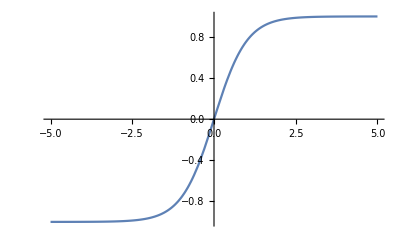

x-x^3/3+(2 x^5)/15+O[x]^6

```mathematica
Plot[Tanh[x],{x, -5, 5}]
Series[Tanh[x], {x, 0, 5}]
```

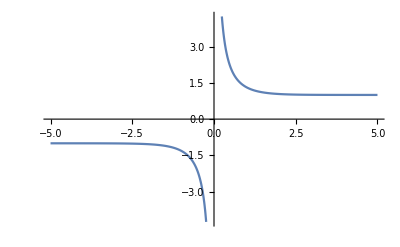

1/x+x/3-x^3/45+(2 x^5)/945+O[x]^6

```mathematica
Plot[Coth[x],{x, -5, 5}]
Series[Coth[x], {x, 0, 5}]
```

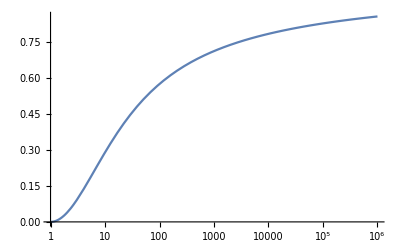

x^2/12-x^4/120+O[x]^5

0.289336

0.574305

0.711049

0.782896

0.826286

0.855235

```mathematica
Δ = 1 - Tanh[Log[κ]/2]/(Log[κ]/2 );
LogLinearPlot[Δ, {κ, 1, 10^6}]
Series[1 - Tanh[x/2]/(x/2 ), {x, 0, 4}]
N[Δ /. {κ-> 10}]
N[Δ /. {κ-> 100}]
N[Δ /. {κ-> 1000}]
N[Δ /. {κ-> 10000}]
N[Δ /. {κ-> 100000}]
N[Δ /. {κ-> 1000000}]
```

```mathematica
Graph[{1<->2,1<->2, 3<->4,5<->6}]
```

-Graphics-